### Todd’s analysis showing rule 22 degrading to rule 146

```mathematica
(*init146=BlockRandom[SeedRandom[30];CellularAutomaton[22,RandomInteger[1,100],{{{2000061}}}]];*)
```

```mathematica
init146={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0};
```

```mathematica
CellularAutomaton[146,init146[[2;;;;2]],80]===CellularAutomaton[22,init146,{{0,160,2},{1,Length[init146],2}}]
```

True

```mathematica
Row[{ArrayPlot[CellularAutomaton[146,init146[[2;;;;2]],80],PixelConstrained->4],ArrayPlot[CellularAutomaton[22,init146,{{0,160,2},{1,Length[init146],2}}],PixelConstrained->4]}]
```

-Graphics--Graphics-

“Maybe saying that rule 22 resists degeneration is better said that it sometimes degenerates, as it did above.”

### what is Todd showing here?:

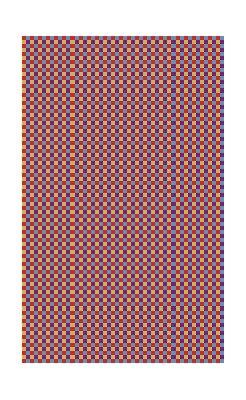

```mathematica
ArrayPlot[Table[(Mod[i,2]+2Mod[j,2])/4,{i,1,81},{j,1,50}],ColorFunction->"Rainbow"]
```

```mathematica
Dimensions[CellularAutomaton[146,init146[[2;;;;2]],80]]
```

{81,50}

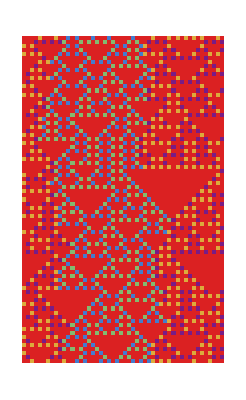

```mathematica
ArrayPlot[MapIndexed[If[#==1,Mod[#2[[1]],2]+2Mod[#2[[2]],2],4]/4&,CellularAutomaton[146,init146[[2;;;;2]],80],{2}],ColorFunction->"Rainbow"]
```

### decompose long rule 22 evolution into even and odd lattice points

“These plots show it not degenerating (probably), where all the dots become one color once it has degenerated.  The offset is chosen (must be odd) to keep the number of points plottable.”

```mathematica
ArrayPlot[CellularAutomaton[22,RandomInteger[1,100],{{1,3000000,9099}}],PixelConstrained->1]
```

-Graphics-

```mathematica
MapIndexed[If[#==1,Mod[#2[[1]]+#2[[2]],2]/.{0->{1,0},1->{0,1}},{0,0}]&,CellularAutomaton[22,RandomInteger[1,100],{{1,3000000,9099}}],{2}]//First
```

{{1,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,1},{1,0},{0,0},{1,0},{0,0},{0,0},{0,0},{1,0},{0,1},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{1,0},{0,0},{1,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,0},{0,0},{0,0},{1,0},{0,0},{0,0},{0,1},{1,0},{0,0},{0,0},{0,0},{1,0},{0,0},{1,0},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,1},{1,0},{0,1},{0,0},{0,0},{0,0},{0,0},{1,0},{0,1},{1,0},{0,0},{1,0},{0,1},{1,0},{0,1},{1,0},{0,0},{1,0},{0,1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,1},{1,0},{0,0}}

### Plot the occupation of even and odd lattice points separately

```mathematica
Transpose[Map[Total,MapIndexed[If[#==1,Mod[#2[[1]]+#2[[2]],2]/.{0->{1,0},1->{0,1}},{0,0}]&,CellularAutomaton[22,RandomInteger[1,100],{{1,3000000,9099}}],{2}]]]
```

{{24,22,13,19,17,13,23,21,23,19,12,14,21,23,14,14,10,16,14,17,17,19,15,21,15,20,18,22,12,15,19,22,15,19,19,23,18,12,17,10,17,20,10,22,25,22,15,15,20,18,18,16,22,30,21,12,28,16,20,12,24,10,24,14,24,14,16,10,20,14,24,14,28,14,24,14,32,14,28,16,16,12,28,14,24,14,24,10,28,14,20,12,28,14,28,10,24,14,20,16,20,12,32,10,24,8,24,12,28,16,32,12,24,16,20,14,28,16,28,12,16,10,32,12,28,10,32,18,24,18,24,14,36,12,24,14,28,14,24,10,24,14,20,14,20,10,32,12,24,16,24,16,28,18,28,12,24,14,28,12,24,14,28,12,24,12,28,12,32,12,20,16,24,12,28,6,28,10,24,16,28,12,24,10,20,8,24,10,24,12,32,12,24,12,24,16,28,12,28,14,20,12,32,10,40,12,28,12,28,10,24,14,28,14,28,12,16,16,20,14,20,14,36,16,28,12,20,14,28,12,24,14,20,10,24,14,20,12,24,16,20,8,24,10,24,14,20,14,28,8,28,12,24,12,20,12,20,18,20,10,24,10,32,12,28,12,28,10,24,16,24,16,24,10,24,10,28,12,20,18,12,8,24,12,28,12,28,12,24,10,16,14,28,12,36,8,28,12,32,12,28,12,36,12,32,12,28,12,24,10,28,14,20,14,24,12,28,8,24,16,24,14,36,16,40,10,32,10,32,12},{21,18,15,21,20,10,17,20,19,20,9,11,13,24,20,23,15,9,15,16,13,17,21,20,16,22,22,18,21,18,23,18,12,18,22,26,21,15,20,14,19,26,18,23,25,17,14,14,18,18,21,14,24,26,16,0,14,0,10,0,12,0,12,0,12,0,8,0,10,0,12,0,14,0,12,0,16,0,14,0,8,0,14,0,12,0,12,0,14,0,10,0,14,0,14,0,12,0,10,0,10,0,16,0,12,0,12,0,14,0,16,0,12,0,10,0,14,0,14,0,8,0,16,0,14,0,16,0,12,0,12,0,18,0,12,0,14,0,12,0,12,0,10,0,10,0,16,0,12,0,12,0,14,0,14,0,12,0,14,0,12,0,14,0,12,0,14,0,16,0,10,0,12,0,14,0,14,0,12,0,14,0,12,0,10,0,12,0,12,0,16,0,12,0,12,0,14,0,14,0,10,0,16,0,20,0,14,0,14,0,12,0,14,0,14,0,8,0,10,0,10,0,18,0,14,0,10,0,14,0,12,0,10,0,12,0,10,0,12,0,10,0,12,0,12,0,10,0,14,0,14,0,12,0,10,0,10,0,10,0,12,0,16,0,14,0,14,0,12,0,12,0,12,0,12,0,14,0,10,0,6,0,12,0,14,0,14,0,12,0,8,0,14,0,18,0,14,0,16,0,14,0,18,0,16,0,14,0,12,0,14,0,10,0,12,0,14,0,12,0,12,0,18,0,20,0,16,0,16,0}}

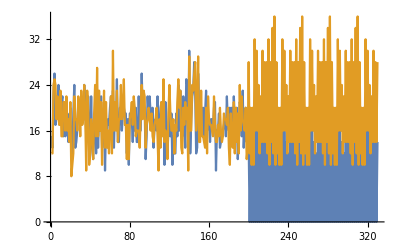

```mathematica
ListPlot[Transpose[Map[Total,MapIndexed[If[#==1,Mod[#2[[1]]+#2[[2]],2]/.{0->{1,0},1->{0,1}},{0,0}]&,CellularAutomaton[22,RandomInteger[1,100],{{1,3000000,9099}}],{2}]]],Joined->True]
```

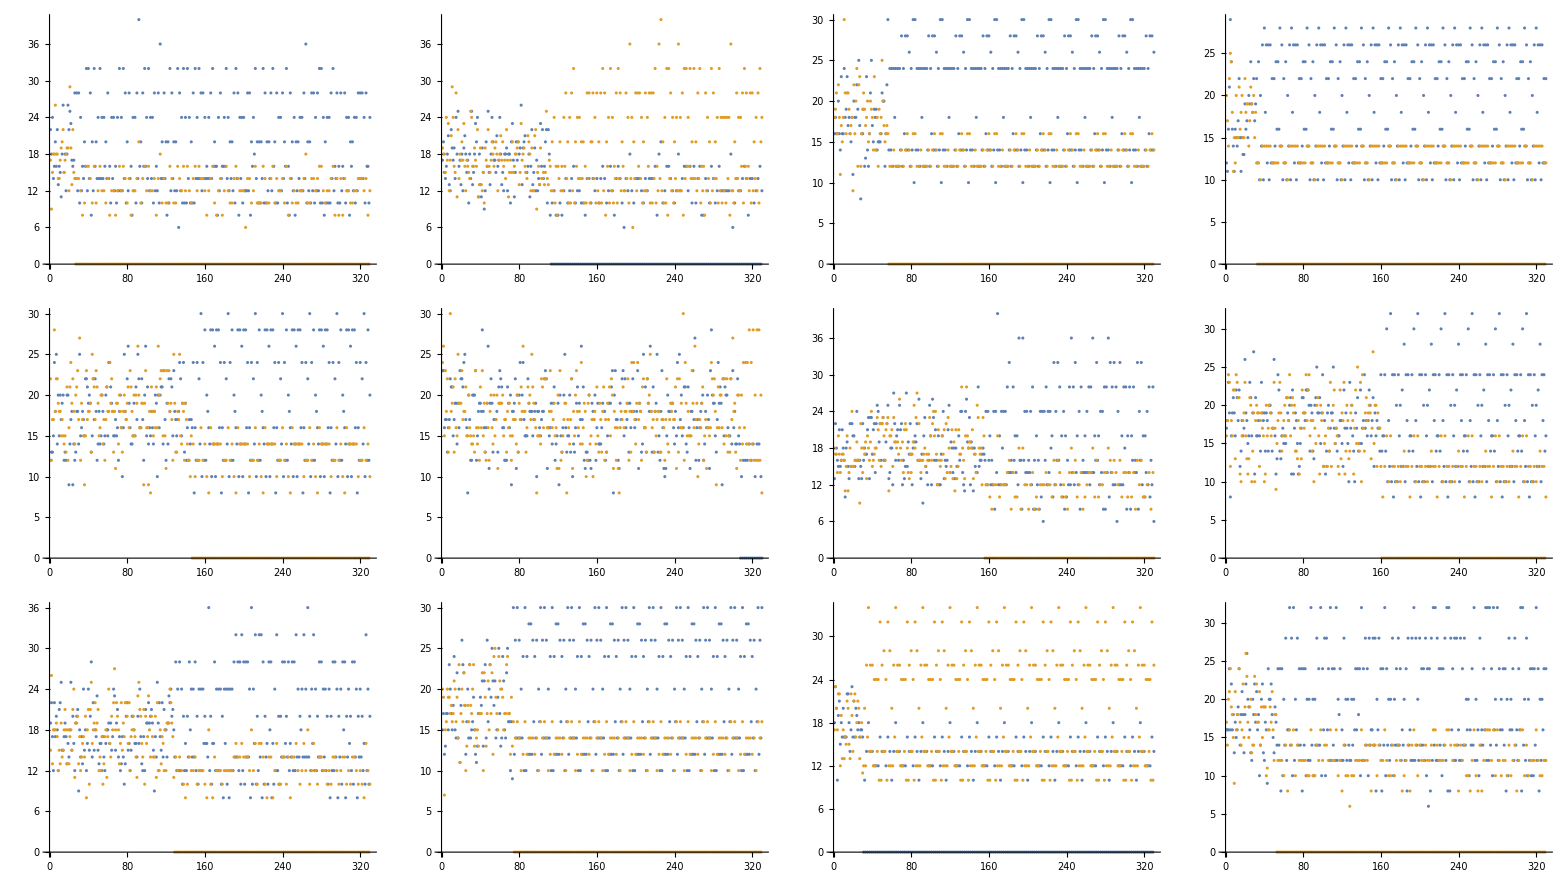

```mathematica
Multicolumn[Table[ListPlot[Transpose[Map[Total,MapIndexed[If[#==1,Mod[#2[[1]]+#2[[2]],2]/.{0->{1,0},1->{0,1}},{0,0}]&,CellularAutomaton[22,RandomInteger[1,100],{{1,3000000,9099}}],{2}]]]],12]]
```